```mathematica
<<PhysicalConstants`
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Needs["ErrorBarPlots`"]
```

DropInList lässt das von einer Liste list mit inneren Listen jedes Element von from bis to fallen (jeweils inklusive)

```mathematica
DropInList[list_,from_,to_]:=Module[{buffer=list}, For[i=0,i<Length[buffer],i++;buffer[[i]]=Drop[buffer[[i]],{from,to}]];If[from⩽to,
Return[buffer],Return["It has to be from =< to"]]]
```

ErrorBarXY erzeugt eine Liste mit ErrorBar[x[[i]],y[[i]]]
Alternativ: ErrorBarXY[listXerr_,listYerr_]=ErrorBar@@@(Partition[Flatten[Riffle[listXerr,listYerr]],2])

```mathematica
ErrorBarXY[listXerr_,listYerr_]:=Module[{buffer=listXerr}, For[i=0,i<Length[buffer],i++;buffer[[i]]=ErrorBar[listXerr[[i]],listYerr[[i]]]]; If[Length[listXerr]==Length[listYerr],
Return[buffer],Return["Length of lists not equal"]]]
```

errorPlotValue erzeugt die Punkte aus listX und listY und hängt jedem Punkt die entsprechende Errorbar[listXerr,listYerr] an

```mathematica
errorPlotValue[listX_,listY_,listXerr_,listYerr_]:=Module[{buffer=listXerr,errors,points,plotValues}, errors=ErrorBarXY[listXerr,listYerr];
points=Partition[Flatten[Riffle[listX,listY]],2];
plotValues=Partition[Riffle[points,errors],2]; If[Length[listXerr]==Length[listYerr]==Length[listX]==Length[listY],
Return[plotValues],Return["Length of lists not equal"]]]
```

errorPropNew ist für die Fehlerfortpflanzung ganzer Listen geeignet. vars={{x,dx},{y,dy}...} und func eine Funktion die von x,y... abhängt. Es wird die zugehörige Fehlerfunktion zurückgegeben. Speicher diese unter einem Namen ab zB errFkt.
Nutze errFkt[f, list_x,list_dx,list_y,list_dy,...]

```mathematica
errorPropNew[func_,vars_]:=Module[{derivs=Table[0,{Length[vars]}],funcErrorForm,parameter,errFunction},

For[ii=1,ii≤Length[vars],ii++,derivs[[ii]]=D[func,vars[[ii,1]]];];
parameter=Flatten[vars];
funcErrorForm=Sqrt[Sum[(derivs[[ii]]*vars[[ii,2]])^2,{ii,Length[vars]}]];
errFunction=Function@@{parameter,funcErrorForm};
Return[errFunction];];
```

Wendet f auf die n-te Komponenten jedes Punktes in g an. Alternativ {f@First[#], Last[#]} &/@ g;

```mathematica
(*  MapAt[(f[#])&,#,n]&/@g   *)
```

## Beispiel: C16

## M1

### Messwerte

```mathematica
messwerte1=({{24.6, 30.3, 35.5, 40.0, 45.0, 50.0, 55.0, 60.0, 65.0, 70.0, 75.0, 80.0, 85.0, 90.0, 95.0, 100.0, 105.0, 110.0, 115.0, 120.0, 125.0, 130.0, 135.4, 140.0, 145.0, 150.0, 155.0, 160.0, 165.0, 170.0}, {1.693, 1.344, 1.090, 0.902, .745, .606, .503, .416, .347, .289, .241, .203, .171, .143, .121, .104, .086, .076, .065, .057, .049, .042, .036, .032, .029, .025, .022, .019, .017, .015}});
```

```mathematica
c=20 *10^-3;
b=10*10^-3;
d=1*10^-3;
```

```mathematica
i1=2.0*10^-3;
```

```mathematica
di1=1.0*10^-3;
```

```mathematica
kB=1.3806504*^-23 ;
```

```mathematica
f[x_]:=x+273.15;
```

```mathematica
messwerte1t=Transpose[messwerte1] ;
```

```mathematica
messwerte1si=MapAt[(f[#])&,#,1]&/@messwerte1t;
```

```mathematica
messwerte1si //MatrixForm ;
```

```mathematica
u1=Transpose[messwerte1si][[2]];
```

```mathematica
leitf[U_]:=i1/U*c/(b *d);
```

```mathematica
leitf1=leitf[#]&/@Transpose[messwerte1si][[2]];
```

```mathematica
g[x_]:=Log[x];
```

```mathematica
leitf1ln=g[#]&/@leitf1;
```

```mathematica
g1[x_]:=1/(2 kB x);
```

```mathematica
messwerte1xaxis=g1[#]&/@Transpose[messwerte1si][[1]];
```

### Fehler

4 stellig U bis 9.999V Auflösung 0.001V Fehler (.5% + 3dgts)

```mathematica
messfehler1u[x_]:=0.001*3+x*0.005;
```

```mathematica
fehler1u=messfehler1u[#] & /@ u1;
```

```mathematica
errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]
```

Function[{U,dU,I1,dI1},√(dI1^2/I1^2+dU^2/U^2)]

```mathematica
leitf1Err=errorPropNew[I1/U*c/(b *d),{{U,dU},{I1,dI1}}]@@{u1,fehler1u,i1,di1};
```

```mathematica
leitf1lnErr=errorPropNew[Log[I1/U*c/(b *d)],{{U,dU},{I1,dI1}}]@@{u1,fehler1u,i1,di1};
```

```mathematica
messfehler1T[x_]:=3+x*0.02;
```

```mathematica
T1GradErr=messfehler1T[#] & /@messwerte1[[1]];
```

```mathematica
errorPropNew[1/(2 kB t),{{t,dt}}];
```

```mathematica
T1K=Transpose[messwerte1si][[1]];
```

```mathematica
messwerte1xaxisErr=errorPropNew[1/(2 kB t),{{t,dt}}]@@{T1K,T1GradErr};
```

### Plotten (Vorbereitung)

```mathematica
points1=Partition[Flatten[Riffle[messwerte1xaxis,leitf1ln]],2];
```

```mathematica
Length[messwerte1xaxis];
```

```mathematica
errors1=Table[ErrorBar[messwerte1xaxisErr[[i ]],leitf1lnErr[[i]]],{i,1,30}];
```

```mathematica
plotValues1=Partition[Riffle[points1,errors1],2];
```

```mathematica
errPlot1=ErrorListPlot[plotValues1,AxesLabel->{"1/(2 SubscriptBox[k, B] T) in 1/J","ln(σ) inA/(V m)"},PlotRange->Full]
```

-Graphics-

```mathematica
messwerte1xaxisErr/messwerte1xaxis;
```

```mathematica
leitf1lnErr/leitf1ln;
```

### Fit (Berechnung)

```mathematica
lmXYErr=LinearModelFit[points1,x,x,Weights->1/(leitf1lnErr^2+(1.1944109069154434*^-19)^2*messwerte1xaxisErr^2),IncludeConstantBasis->True];
```

```mathematica
lmYErr=LinearModelFit[points1,x,x,Weights->1/leitf1lnErr^2,IncludeConstantBasis->True];
```

```mathematica
Show[errPlot1, Plot[{Normal[lmYErr]},{x,0,10^21}, PlotLegends->{"Y Error: " <> ToString[lmYErr["BestFit"]]},PlotStyle->{Black}]]
```

-Graphics-

```mathematica
lmYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{15.2786-1.19441×10^-19 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 15.2786 | 0.0648676 | 235.534 | 1.03327×10^-47
x | -1.19441×10^-19 | 6.48191×10^-22 | -184.268 | 9.93657×10^-45, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 228.278 | 228.278 | 33954.8 | 9.93657×10^-45
Error | 28 | 0.188244 | 0.00672299 |  | 
Total | 29 | 228.466 |  |  | ,0.999176,0.999147}

```mathematica
Show[errPlot1, Plot[{Normal[lmXYErr]},{x,0,10^21}, PlotLegends->{"XY Error: " <> ToString[lmNew["BestFit"]]},PlotStyle->{Black}]]
```

-Graphics-

```mathematica
lmXYErr[{"BestFit","ParameterTable","ANOVATable","RSquared","AdjustedRSquared"}]
```

{15.2822-1.19476×10^-19 x, | Estimate | Standard Error | t-Statistic | P-Value
1 | 15.2822 | 0.064698 | 236.208 | 9.53933×10^-48
x | -1.19476×10^-19 | 6.47398×10^-22 | -184.549 | 9.52249×10^-45, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 208.261 | 208.261 | 34058.3 | 9.52249×10^-45
Error | 28 | 0.171215 | 0.00611484 |  | 
Total | 29 | 208.432 |  |  | ,0.999179,0.999149}

```mathematica
Exp[15.282159935452153]
```

4.33469×10^6

```mathematica
errorPropNew[Exp[x],{{x,dx}}]@@{15.282159935452153,0.06469799300769175}
```

280446.

```mathematica
%/10^6
```

0.280446

E_G= (1.19441+-0.006481)*10^-19 nur X Gewicht

E_G= (1.1948+-0.0065)*10^-19 X und Y Gewicht und σ_0= (4.33 +- 0.28 )×10^6

```mathematica
0.0065/1.1948
```

0.00544024

```mathematica
(.28)/4.33
```

0.0646651

# SLOT

## Versuch 2

```mathematica
kontrast[iMax_,iMin_]:= (iMax - iMin)/(iMax + iMin)
```

```mathematica
resolutionUSAF[gruppe_,element_]:=2^(gruppe+(element -1)/6)
```

```mathematica
l=Table[i,{i,1,6}];
```

```mathematica
kontrastMinus[iMax_,iMin_]:= (iMax + iMin)/(iMax - iMin)
```

```mathematica
kontrast[562,67]//N
```

0.786963

```mathematica
kontrastMinus[377,-122]//N
```

0.511022

```mathematica
kontrast[170,34]//N
```

0.666667

```mathematica
kontrast[158,22]//N
```

0.755556

## Messwerte

```mathematica
jn24502jnMinusdIIIgruppe2=({{556, 69}, {401, 50}, {433, 56}, {459, 59}, {469, 65}, {474, 78}});
```

```mathematica
jn24502jnMinusdIIIgruppe3=({{405, 74}, {418, 80}});
```

```mathematica
jn24502jnMinusdgruppe2=({{563, 68}, {421, 56}, {459, 57}, {491, 57}, {508, 58}, {500, 72}});
```

```mathematica
jn24502jnMinusdgruppe3=({{310, 81}, {372, 130}});
```

```mathematica
jn24502nnMinusdIIIgruppe2=({{449, 178}, {329, 166}, {339, 185}, {338, 219}, {330, 237}, {325, 260}});
```

```mathematica
jn24502nnMinusdIIIgruppe3=({{317, 250}, {334, 276}});
```

```mathematica
jn24502nnMinusdgruppe2=({{395, 227}, {302, 209}, {306, 241}, {326, 260}, {313, 274}, {307, 293}});
```

```mathematica
jn24502nnMinusdgruppe3=({{305, 265}, {311, 300}});
```

```mathematica
jn14502jnMinusdgruppe4=({{158, 22}, {147, 22}, {147, 24}, {147, 26}, {144, 28}, {142, 31}});
```

```mathematica
jn14502jnMinusdgruppe5=({{130, 36}, {128, 41}, {120, 44}, {113, 54}, {101, 59}, {101, 67}});
```

```mathematica
jn14502jnMinusdgruppe6=({{94, 73}, {87, 76}, {83, 76}, {□, □}, {□, □}, {□, □}});
```

```mathematica
jn14502jnMinusdIIIgruppe4=({{154, 26}, {142, 26}, {141, 28}, {140, 31}, {136, 35}, {133, 39}});
```

```mathematica
jn14502jnMinusdIIIgruppe5=({{123, 42}, {117, 49.5}, {111, 55}, {105, 60}, {100.5, 65}, {94.6, 71}});
```

```mathematica
jn14502jnMinusdIIIgruppe6=({{90, 74}, {85, 75}, {79, 77}, {□, □}, {□, □}, {□, □}});
```

```mathematica
jn15202jnMinusdIIIgruppe4=({{329, 54}, {303, 54}, {298, 61}, {294, 68}, {284, 80}, {272, 92}});
```

```mathematica
jn15202jnMinusdIIIgruppe5=({{250, 99.5}, {237, 112}, {224, 124}, {211, 138}, {198, 146}, {187, 156}});
```

```mathematica
jn15202jnMinusdIIIgruppe6=({{179, 162}, {168, 162}, {□, □}, {□, □}, {□, □}, {□, □}});
```

```mathematica
jn15202jnMinusdgruppe4=({{353, 49}, {332, 48}, {329, 51}, {332, 60}, {324, 61}, {320, 69}});
```

```mathematica
jn15202jnMinusdgruppe5=({{269, 73}, {276, 88}, {246, 115}, {243, 115}, {226, 136}, {209, 147}});
```

```mathematica
jn15202jnMinusdgruppe6=({{□, □}, {□, □}, {□, □}, {□, □}, {□, □}, {□, □}});
```

```mathematica
jn25202jnMinusdIIIgruppe2=({{356, 38}, {257, 28}, {275, 31}, {288, 35}, {298, 38}, {306, 46}});
```

```mathematica
jn25202jnMinusdIIIgruppe3=({{242, 65}, {241, 82}, {225, 125}, {224, 122}, {251, 108}, {234, 135}});
```

```mathematica
jn25202jnMinusdgruppe2=({{362, 30}, {274, 23}, {294, 26}, {315, 28}, {326, 31}, {333, 33}});
```

```mathematica
jn25202jnMinusdgruppe3=({{235, 72}, {296, 33}, {254, 50}, {304, 57}});
```

```mathematica
jn24505jnMinusdIIIgruppe2=({{773, 90}, {623, 87}, {666, 94}, {680, 92}, {680, 105}, {603, 153}});
```

```mathematica
jn24505jnMinusdIIIgruppe3=({{562, 152}, {550, 207}, {621, 238}, {496, 314}, {519, 253}, {514, 308}});
```

```mathematica
jn24505jnMinusdgruppe2=({{769, 89}, {549, 87}, {644, 88}, {570, 98}, {660, 124}, {568, 247}});
```

```mathematica
jn24505jnMinusdgruppe3=({{568, 151}, {584, 247}, {591, 132}, {□, □}, {□, □}, {□, □}});
```

```mathematica
jn14505jnMinusdIIIgruppe4=({{698, 125}, {656, 121}, {657.6, 125}, {651, 131}, {647, 141}, {638, 155.5}});
```

```mathematica
jn14505jnMinusdIIIgruppe5=({{627, 174.5}, {614, 185}, {597, 196}, {565, 213}, {552, 221}, {531, 239}});
```

```mathematica
jn14505jnMinusdIIIgruppe6=({{467, 277}, {441, 276}, {403, 300}, {400, 307}, {382, 301}, {□, □}});
```

```mathematica
jn14505jnMinusdgruppe4=({{710, 112}, {608, 106}, {675, 109}, {669, 116}, {679, 122}, {671, 129}});
```

```mathematica
jn14505jnMinusdgruppe5=({{655, 135}, {663, 144}, {615, 171}, {639, 160}, {601, 186}, {598, 197}});
```

```mathematica
jn14505jnMinusdgruppe6=({{559, 207}, {498, 247}, {425, 285}, {450, 250}, {409, 295}, {401, 312}});
```

```mathematica
kontrast[79,77]//N
```

0.0128205

Für Plot von Gruppe 2,3

```mathematica
linien2={jn24502jnMinusdIIIgruppe2,jn24502jnMinusdgruppe2,jn24502nnMinusdIIIgruppe2,jn24502nnMinusdgruppe2,jn25202jnMinusdIIIgruppe2,jn25202jnMinusdgruppe2,jn24505jnMinusdIIIgruppe2,jn24505jnMinusdgruppe2};
```

```mathematica
linien3={jn24502jnMinusdIIIgruppe3,jn24502jnMinusdgruppe3,jn24502nnMinusdIIIgruppe3,jn24502nnMinusdgruppe3,jn25202jnMinusdIIIgruppe3,jn25202jnMinusdgruppe3,jn24505jnMinusdIIIgruppe3,jn24505jnMinusdgruppe3};
```

```mathematica
yAllgemein=Table[Join[kontrast@@@linien2[[n]],kontrast@@@linien3[[n]]],{n,1,Length[linien2]}];//N
```

```mathematica
xAllgemein=Table[Join[resolutionUSAF[2,#]&/@Table[i,{i,1,Length[jn24502jnMinusdIIIgruppe2]}],resolutionUSAF[3,#]&/@Table[i,{i,1,Length[jn24502jnMinusdIIIgruppe3]}]],{n,1,Length[linien2]}];//N
```

Für Plot von Gruppe 4,5,6

```mathematica
linien4={jn14502jnMinusdgruppe4,jn14502jnMinusdIIIgruppe4,jn15202jnMinusdIIIgruppe4,jn15202jnMinusdgruppe4,jn14505jnMinusdIIIgruppe4,jn14505jnMinusdgruppe4};
linien5={jn14502jnMinusdgruppe5,jn14502jnMinusdIIIgruppe5,jn15202jnMinusdIIIgruppe5,jn15202jnMinusdgruppe5,jn14505jnMinusdIIIgruppe5,jn14505jnMinusdgruppe5};
linien6={jn14502jnMinusdgruppe6,jn14502jnMinusdIIIgruppe6,jn15202jnMinusdIIIgruppe6, jn15202jnMinusdgruppe6,jn14505jnMinusdIIIgruppe6,jn14505jnMinusdgruppe6};
```

```mathematica
y1Allgemein=Table[Join[kontrast@@@linien4[[n]],kontrast@@@linien5[[n]],kontrast@@@linien6[[n]]],{n,1,Length[linien6]}];//N
```

```mathematica
x1Allgemein=Table[Join[resolutionUSAF[4,#]&/@Table[i,{i,1,Length[jn14502jnMinusdgruppe4]}],resolutionUSAF[5,#]&/@Table[i,{i,1,Length[jn14502jnMinusdgruppe5]}] ,resolutionUSAF[6,#]&/@Table[i,{i,1,Length[jn14502jnMinusdgruppe6]}] ],{n,1,Length[linien6]}];//N
```

Für Plot mit Horizontal-Auflösung

```mathematica
linien4III={jn14505jnMinusdIIIgruppe4,jn14502jnMinusdIIIgruppe4,jn15202jnMinusdIIIgruppe4};
linien5III={jn14505jnMinusdIIIgruppe5,jn14502jnMinusdIIIgruppe5,jn15202jnMinusdIIIgruppe5};
linien6III={jn14505jnMinusdIIIgruppe6,jn14502jnMinusdIIIgruppe6,jn15202jnMinusdIIIgruppe6};
```

```mathematica
yIIIAllgemein=Table[Join[kontrast@@@linien4III[[n]],kontrast@@@linien5III[[n]],kontrast@@@linien6III[[n]]],{n,1,Length[linien6III]}];//N
```

```mathematica
xIIIAllgemein=Table[Join[resolutionUSAF[4,#]&/@Table[i,{i,1,Length[jn14502jnMinusdIIIgruppe4]}],resolutionUSAF[5,#]&/@Table[i,{i,1,Length[jn14502jnMinusdIIIgruppe5]}] ,resolutionUSAF[6,#]&/@Table[i,{i,1,Length[jn14502jnMinusdIIIgruppe6]}] ],{n,1,Length[linien6III]}];//N
```

Für Plot mit Vertikal - Auflösung

```mathematica
linien4v={jn14505jnMinusdgruppe4,jn14502jnMinusdgruppe4,jn15202jnMinusdgruppe4};
linien5v={jn14505jnMinusdgruppe5,jn14502jnMinusdgruppe5,jn15202jnMinusdgruppe5};
linien6v={jn14505jnMinusdgruppe6,jn14502jnMinusdgruppe6,jn15202jnMinusdgruppe6};
```

```mathematica
yvAllgemein=Table[Join[kontrast@@@linien4v[[n]],kontrast@@@linien5v[[n]],kontrast@@@linien6v[[n]]],{n,1,Length[linien6v]}];//N
```

```mathematica
xvAllgemein=Table[Join[resolutionUSAF[4,#]&/@Table[i,{i,1,Length[jn14502jnMinusdgruppe4]}],resolutionUSAF[5,#]&/@Table[i,{i,1,Length[jn14502jnMinusdgruppe5]}] ,resolutionUSAF[6,#]&/@Table[i,{i,1,Length[jn14502jnMinusdgruppe6]}] ],{n,1,Length[linien6v]}];//N
```

## Plotten Allgemein

Für Plot von Gruppe 2,3

```mathematica
SLOTpointsAllgemein=Table[Partition[Flatten[Riffle[xAllgemein[[i]],yAllgemein[[i]]]],2],{i,1,Length[linien2]}]; //N
```

```mathematica
SLOTxErr=Table[0,{i,1,12}];
```

```mathematica
SLOTyErr=Table[0,{i,1,12}];
```

```mathematica
SLOTerr=Table[ErrorBar[SLOTxErr[[i ]],SLOTyErr[[i]]],{i,1,12}];
```

```mathematica
plotSLOTAllgemein=Table[Partition[Riffle[SLOTpointsAllgemein[[i]],SLOTerr],2],{i,1,Length[linien2]}];
```

```mathematica
legendeAllgemein={"λ=450 ⌀=2 III Gruppe 2","λ=450 ⌀=2 Gruppe 2","λ=520 ⌀=2 unfokussiert III Gruppe 2","λ=450 ⌀=2 unfokussiert Gruppe2"};
```

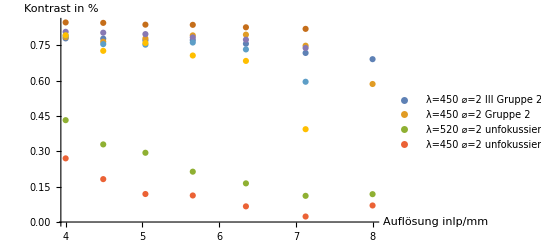

```mathematica
errPlotAllgemein=ErrorListPlot[plotSLOTAllgemein,AxesLabel->{"Auflösung inlp/mm","Kontrast in %"},PlotRange->Full,PlotLegends-> legendeAllgemein]
```

Für Plot von Gruppe 4, 5, 6

```mathematica
SLOTpoints1Allgemein=Table[Partition[Flatten[Riffle[x1Allgemein[[i]],y1Allgemein[[i]]]],2],{i,1,Length[linien6]}];
```

```mathematica
SLOTx1Err=Table[0,{i,1,Length[x1Allgemein[[2]]]}];
```

```mathematica
SLOTy1Err=Table[0,{i,1,Length[x1Allgemein[[2]]]}];
```

```mathematica
SLOT1err=Table[ErrorBar[SLOTx1Err[[i ]],SLOTy1Err[[i]]],{i,1,Length[x1Allgemein[[1]]]}];
```

```mathematica
plotSLOT1Allgemein=Table[Partition[Riffle[SLOTpoints1Allgemein[[i]],SLOT1err],2],{i,1,Length[linien6]}];
```

```mathematica
legende1Allgemein={"λ=450 ⌀=2","λ=450 ⌀=2 III","λ=520 ⌀=2 III","λ=520 ⌀=2","λ=450 ⌀=5 III","λ=450 ⌀=5"};
```

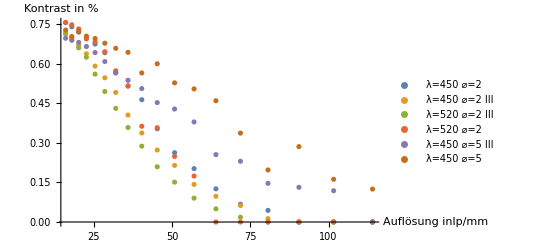

```mathematica
errPlot1Allgemein=ErrorListPlot[plotSLOT1Allgemein,AxesLabel->{"Auflösung inlp/mm","Kontrast in %"},PlotRange->Full,PlotLegends-> legende1Allgemein]
```

Für Plot mit Horizontal - Auflösung

```mathematica
SLOTpointsIIIAllgemein=Table[Partition[Flatten[Riffle[xIIIAllgemein[[i]],yIIIAllgemein[[i]]]],2],{i,1,Length[linien6III]}];
```

```mathematica
SLOTxIIIErr=Table[0,{i,1,Length[xIIIAllgemein[[1]]]}];
```

```mathematica
SLOTyIIIErr=Table[0,{i,1,Length[xIIIAllgemein[[1]]]}];
```

```mathematica
SLOTIIIerr=Table[ErrorBar[SLOTxIIIErr[[i ]],SLOTyIIIErr[[i]]],{i,1,Length[xIIIAllgemein[[1]]]}];
```

```mathematica
plotSLOTIIIAllgemein=Table[Partition[Riffle[SLOTpointsIIIAllgemein[[i]],SLOTIIIerr],2],{i,1,Length[linien6III]}];
```

```mathematica
legendeIIIAllgemein={"λ=450 ⌀=5 III","λ=450 ⌀=2 III","λ=520 ⌀=2 III"};
```

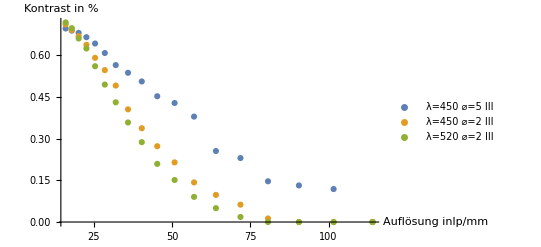

```mathematica
errPlotIIIAllgemein=ErrorListPlot[plotSLOTIIIAllgemein,AxesLabel->{"Auflösung inlp/mm","Kontrast in %"},PlotRange->Full,PlotLegends-> legendeIIIAllgemein]
```

Für Plot mit Vertikal - Auflösung

```mathematica
SLOTpointsvAllgemein=Table[Partition[Flatten[Riffle[xvAllgemein[[i]],yvAllgemein[[i]]]],2],{i,1,Length[linien6v]}] //N
```

{{{16.,0.727494},{17.9594,0.703081},{20.1587,0.721939},{22.6274,0.704459},{25.3984,0.695381},{28.5088,0.6775},{32.,0.658228},{35.9188,0.643123},{40.3175,0.564885},{45.2548,0.599499},{50.7968,0.527319},{57.0175,0.504403},{64.,0.45953},{71.8376,0.336913},{80.6349,0.197183},{90.5097,0.285714},{101.594,0.161932},{114.035,0.124825}},{{16.,0.755556},{17.9594,0.739645},{20.1587,0.719298},{22.6274,0.699422},{25.3984,0.674419},{28.5088,0.641618},{32.,0.566265},{35.9188,0.514793},{40.3175,0.463415},{45.2548,0.353293},{50.7968,0.2625},{57.0175,0.202381},{64.,0.125749},{71.8376,0.0674847},{80.6349,0.0440252},{90.5097,0.},{101.594,0.},{114.035,0.}},{{16.,0.756219},{17.9594,0.747368},{20.1587,0.731579},{22.6274,0.693878},{25.3984,0.683117},{28.5088,0.645244},{32.,0.573099},{35.9188,0.516484},{40.3175,0.362881},{45.2548,0.357542},{50.7968,0.248619},{57.0175,0.174157},{64.,0.},{71.8376,0.},{80.6349,0.},{90.5097,0.},{101.594,0.},{114.035,0.}}}

```mathematica
SLOTxvErr=Table[0,{i,1,Length[xvAllgemein[[2]]]}];
```

```mathematica
SLOTyvErr=Table[0,{i,1,Length[xvAllgemein[[2]]]}];
```

```mathematica
SLOTverr=Table[ErrorBar[SLOTxvErr[[i ]],SLOTyvErr[[i]]],{i,1,Length[xvAllgemein[[1]]]}];//N
```

```mathematica
plotSLOTvAllgemein=Table[Partition[Riffle[SLOTpointsvAllgemein[[i]],SLOTverr],2],{i,1,Length[linien6v]}];
```

```mathematica
legendevAllgemein={"λ=450 ⌀=5","λ=450 ⌀=2","λ=520 ⌀=2"};
```

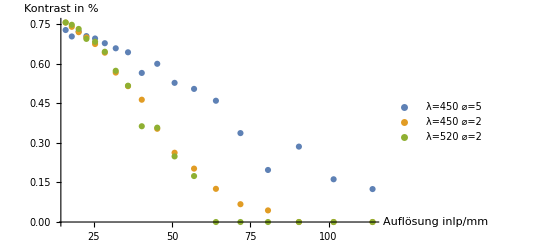

```mathematica
errPlotvAllgemein=ErrorListPlot[plotSLOTvAllgemein,AxesLabel->{"Auflösung inlp/mm","Kontrast in %"},PlotRange->Full,PlotLegends-> legendevAllgemein]
```

## Ausprobieren

### Listen für jn und nn

```mathematica
y2=kontrast@@@jn24502jnMinusdIIIgruppe2//N
```

{0.7792,0.778271,0.770961,0.772201,0.756554,0.717391}

```mathematica
x2=resolutionUSAF[2,#]&/@l //N
```

{4.,4.48985,5.03968,5.65685,6.3496,7.12719}

```mathematica
y3=kontrast@@@jn24502jnMinusdIIIgruppe3//N
```

{0.691023,0.678715}

```mathematica
x3=resolutionUSAF[3,#]&/@Table[i,{i,1,2}] //N
```

{8.,8.9797}

```mathematica
x=Join[x2,x3]
```

{4.,4.48985,5.03968,5.65685,6.3496,7.12719,8.,8.9797}

```mathematica
y=Join[y2,y3]
```

{0.7792,0.778271,0.770961,0.772201,0.756554,0.717391,0.691023,0.678715}

### Plot jn

```mathematica
SLOTpoints=Partition[Flatten[Riffle[x,y]],2];
```

```mathematica
Length[x]
```

8

```mathematica
SLOTxErr=Table[0,{i,1,8}];
```

```mathematica
SLOTyErr=Table[0,{i,1,8}];
```

```mathematica
SLOTerr=Table[ErrorBar[SLOTxErr[[i ]],SLOTyErr[[i]]],{i,1,8}];
```

```mathematica
plotSLOT=Partition[Riffle[SLOTpoints,SLOTerr],2];
```

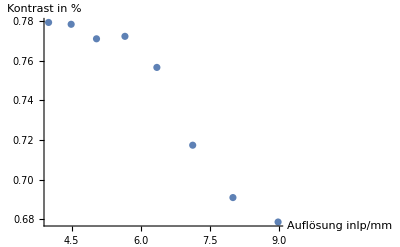

```mathematica
errPlot1=ErrorListPlot[plotSLOT,AxesLabel->{"Auflösung inlp/mm","Kontrast in %"},PlotRange->Full]
```

### Plot nn

```mathematica
Ny2=kontrast@@@jn24502nnMinusdIIIgruppe2//N
```

{0.432217,0.329293,0.293893,0.213645,0.164021,0.111111}

```mathematica
Nx2=resolutionUSAF[2,#]&/@l //N
```

{4.,4.48985,5.03968,5.65685,6.3496,7.12719}

```mathematica
Ny3=kontrast@@@jn24502nnMinusdIIIgruppe3//N
```

{0.118166,0.095082}

```mathematica
Nx3=resolutionUSAF[3,#]&/@Table[i,{i,1,2}] //N
```

{8.,8.9797}

```mathematica
Nx=Join[Nx2,Nx3]
```

{4.,4.48985,5.03968,5.65685,6.3496,7.12719,8.,8.9797}

```mathematica
Ny=Join[Ny2,Ny3]
```

{0.432217,0.329293,0.293893,0.213645,0.164021,0.111111,0.118166,0.095082}

```mathematica
NSLOTpoints=Partition[Flatten[Riffle[Nx,Ny]],2];
```

```mathematica
SLOTxErr=Table[0,{i,1,8}];
```

```mathematica
SLOTyErr=Table[0,{i,1,8}];
```

```mathematica
NSLOTerr=Table[ErrorBar[SLOTxErr[[i ]],SLOTyErr[[i]]],{i,1,8}];
```

```mathematica
NplotSLOT=Partition[Riffle[NSLOTpoints,NSLOTerr],2];
```

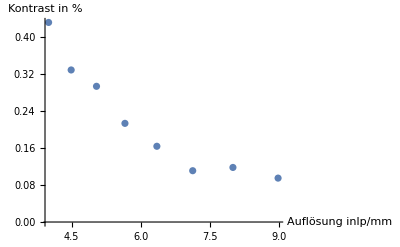

```mathematica
NerrPlot1=ErrorListPlot[NplotSLOT,AxesLabel->{"Auflösung inlp/mm","Kontrast in %"},PlotRange->Full]
```